```mathematica
randomstep:=RandomReal[{0,1}] Through[{Cos,Sin}[RandomReal[{0,2Pi}]]];

rndwalk[numpts_,streakiness_,numruns_]:=Module[{streak},
Table[streak=streakiness randomstep;
RandomChoice[{Identity,Reverse}]@NestList[#+streak+0.1 randomstep&,randomstep,numpts],{numruns}]];

spatter[points_]:=ImagePad[
Rasterize@
Graphics[
Thread[
Disk[#,Range[(Length@#-1),0,-1]/(10. (Length@#-1))]]&/@points],50,1];

imageprocess[pic_,filterwidth_,threshold_,droplets_,reflect_]:=Module[{smoothed,combined},smoothed=Binarize[GaussianFilter[pic,filterwidth],threshold];
combined=If[droplets,ImageMultiply[smoothed,pic],smoothed];
If[reflect,ImageMultiply[combined,ImageReflect[combined,Left]],combined]];

Manipulate[SeedRandom[seed];
imageprocess[spatter[rndwalk[numpts,streakiness,numspatters]],filterwidth,threshold,droplets,reflect],{{seed,0},0,10^6,1},{{numpts,100},10,300,1},{{streakiness,0},0,0.05},{{numspatters,10},1,20,1},{{filterwidth,10},1,20},{{threshold,0.6},0,1},{{droplets,True},{True,False}},{{reflect,True},{True,False}}];
```

```mathematica
{Cos,Sin}@{{0,1},{-1,-1},{0,0}}
```

{Cos,Sin}[{{0,1},{-1,-1},{0,0}}]

```mathematica
a={{0,1},{-1,-1},{0,0}}
```

{{0,1},{-1,-1},{0,0}}

```mathematica
{ArcCos[a[[All,1]]],ArcSin[a[[All,2]]]}
```

{{π/2,π,π/2},{π/2,-π/2,0}}

```mathematica
a=Flatten[rndwalk[5,1,3],1]
```

{{-1.99441,1.86221},{-1.7407,1.49784},{-1.3755,1.16851},{-1.02479,0.837051},{-0.705991,0.51447},{-0.379997,0.1741},{4.08338,-0.579748},{3.32663,-0.584827},{2.42287,-0.51428},{1.66056,-0.491667},{0.857883,-0.487178},{0.0462196,-0.474965},{-0.133695,-0.663416},{-0.076091,-0.45626},{0.00666977,-0.136101},{0.0149545,0.118913},{-0.0412387,0.40465},{-0.0239432,0.669589}}

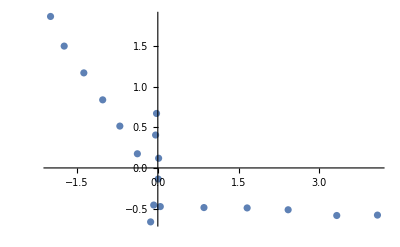

```mathematica
ListPlot[a]
```